```mathematica
exp227rawdata=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{1.26221,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{22.4097,Null}

```mathematica
comblintestexp227=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{59.4601,Null}

```mathematica
comblinmultiplytestexp227=combinelineagesmulitply2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{53.5334,Null}

```mathematica
Length[comblinmultiplytestexp227]
```

799

```mathematica
MatrixForm[comblinmultiplytestexp227[[799]][[1;;10]]]
```

(799 | 13255 | 5.2 | 14 | 90 | 3546.72 | 363.656
799 | 13255 | 5.21667 | 12 | 81 | 3735.44 | 343.012
799 | 13255 | 5.23333 | 14 | 93 | 3490.17 | 330.505
799 | 13255 | 5.25 | 13 | 86 | 3491.34 | 365.605
799 | 13255 | 5.26667 | 13 | 85 | 3521.81 | 349.153
799 | 13255 | 5.28333 | 14 | 88 | 3724.98 | 366.489
799 | 13255 | 5.3 | 13 | 89 | 3674.37 | 359.18
799 | 13255 | 5.31667 | 13 | 83 | 3569.58 | 308.831
799 | 13255 | 5.33333 | 14 | 88 | 3570.14 | 335.568
799 | 13255 | 5.35 | 14 | 87 | 3583.82 | 330.391)

```mathematica
sets=Partition[RandomSample[Range[799]],266,266,267];
```

```mathematica
comblinset1=Map[comblintestexp227[[#]]&,sets[[1]]];
```

```mathematica
comblinset2=Map[comblintestexp227[[#]]&,sets[[2]]];comblinset3=Map[comblintestexp227[[#]]&,sets[[3]]];
```

```mathematica
comblinmultiplyset1=Map[comblinmultiplytestexp227[[#]]&,sets[[1]]];
```

```mathematica
comblinmultiplyset2=Map[comblinmultiplytestexp227[[#]]&,sets[[2]]];comblinmultiplyset3=Map[comblinmultiplytestexp227[[#]]&,sets[[3]]];
```

```mathematica
growthset1noextrap=growthratecalcsupnoextrap[comblinmultiplyset1,30,comblinset1];//AbsoluteTiming
```

266

{3.0838,Null}

```mathematica
growthset2noextrap=growthratecalcsupnoextrap[comblinmultiplyset2,30,comblinset2];//AbsoluteTiming
```

266

{3.43791,Null}

```mathematica
growthset3noextrap=growthratecalcsupnoextrap[comblinmultiplyset3,30,comblinset3];//AbsoluteTiming
```

266

{2.63318,Null}

```mathematica
growthset1cellphasenoextrap=addcellphase[growthset1noextrap];//AbsoluteTiming
```

{0.0989836,Null}

```mathematica
growthset2cellphasenoextrap=addcellphase[growthset2noextrap];//AbsoluteTiming
growthset3cellphasenoextrap=addcellphase[growthset3noextrap];//AbsoluteTiming
```

{0.10198,Null}

{0.0671172,Null}

```mathematica
avgcellphaseset1nofit=averagecellphasenofitting[growthset1cellphasenoextrap,20];
```

```mathematica
avgcellphaseset2nofit=averagecellphasenofitting[growthset2cellphasenoextrap,20];
avgcellphaseset3nofit=averagecellphasenofitting[growthset3cellphasenoextrap,20];
```

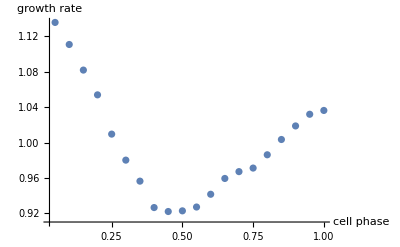

```mathematica
ListPlot[avgcellphaseacetatenofit[[All,{1,2}]],AxesLabel->{"cell phase","growth rate"},PlotRange->All]
```

```mathematica
avgcellphaseset1noextrap=averagecellphase[growthset1cellphasenoextrap,growthset1noextrap];//AbsoluteTiming
```

{37.5452,Null}

```mathematica
avgcellphaseset2noextrap=averagecellphase[growthset2cellphasenoextrap,growthset2noextrap];//AbsoluteTiming
```

{43.5936,Null}

```mathematica
avgcellphaseset3noextrap=averagecellphase[growthset3cellphasenoextrap,growthset3noextrap];//AbsoluteTiming
```

{23.3153,Null}

```mathematica
normcellphaseset1noextrap=normcellphase[avgcellphaseset1noextrap,growthset1cellphasenoextrap];//AbsoluteTiming
```

{0.599871,Null}

```mathematica
normcellphaseset2noextrap=normcellphase[avgcellphaseset2noextrap,growthset2cellphasenoextrap];//AbsoluteTiming
```

{0.643716,Null}

```mathematica
normcellphaseset3noextrap=normcellphase[avgcellphaseset3noextrap,growthset3cellphasenoextrap];//AbsoluteTiming
```

{0.503675,Null}

```mathematica
combnormcellphaseset1noextrap=combnormcellphase[normcellphaseset1noextrap,growthset1noextrap];//AbsoluteTiming
```

{0.315922,Null}

```mathematica
combnormcellphaseset2noextrap=combnormcellphase[normcellphaseset2noextrap,growthset2noextrap];//AbsoluteTiming
```

{0.332235,Null}

```mathematica
combnormcellphaseset3noextrap=combnormcellphase[normcellphaseset3noextrap,growthset3noextrap];//AbsoluteTiming
```

{0.264272,Null}

```mathematica
{avggrowthplotset1noextrap,avgmcplotset1noextrap,avgbetaxplotset1noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphaseset1noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphaseset1noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphaseset1noextrap]]};//AbsoluteTiming
```

{12.3369,Null}

```mathematica
{avggrowthplotset2noextrap,avgmcplotset2noextrap,avgbetaxplotset2noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphaseset2noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphaseset2noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphaseset2noextrap]]};//AbsoluteTiming
```

{13.9082,Null}

```mathematica
{avggrowthplotset3noextrap,avgmcplotset3noextrap,avgbetaxplotset3noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphaseset3noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphaseset3noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphaseset3noextrap]]};//AbsoluteTiming
```

{11.3146,Null}

```mathematica
Mean[avggrowthplotacetatenoextrap[[All,2]]]
```

0.733447

```mathematica
Log[2]/0.733*60
```

56.7378

```mathematica
{set1growthwithrepeatnoextrap,set1growthwithrepeatnosubnoextrap,set1mcwithrepeatnoextrap,set1mcwithrepeatnosubnoextrap,set1betaxwithrepeatnoextrap,set1betaxwithrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,10,avggrowthplotset1noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,11,avgmcplotset1noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,12,avgbetaxplotset1noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphaseset1noextrap,12,0],12,5]};//AbsoluteTiming
```

{42.5514,Null}

```mathematica
{set2growthwithrepeatnoextrap,set2growthwithrepeatnosubnoextrap,set2mcwithrepeatnoextrap,set2mcwithrepeatnosubnoextrap,set2betaxwithrepeatnoextrap,set2betaxwithrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,10,avggrowthplotset2noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,11,avgmcplotset2noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,12,avgbetaxplotset2noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphaseset2noextrap,12,0],12,5]};//AbsoluteTiming
```

{45.9174,Null}

```mathematica
{set3growthwithrepeatnoextrap,set3growthwithrepeatnosubnoextrap,set3mcwithrepeatnoextrap,set3mcwithrepeatnosubnoextrap,set3betaxwithrepeatnoextrap,set3betaxwithrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,10,avggrowthplotset3noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,11,avgmcplotset3noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,12,avgbetaxplotset3noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphaseset3noextrap,12,0],12,5]};//AbsoluteTiming
```

{36.9034,Null}

```mathematica
SetSharedVariable[set1growthwithrepeatnoextrap,set1growthwithrepeatnosubnoextrap,set1mcwithrepeatnoextrap,set1mcwithrepeatnosubnoextrap,set1betaxwithrepeatnoextrap,set1betaxwithrepeatnosubnoextrap];
```

```mathematica
SetSharedVariable[set2growthwithrepeatnoextrap,set2growthwithrepeatnosubnoextrap,set2mcwithrepeatnoextrap,set2mcwithrepeatnosubnoextrap,set2betaxwithrepeatnoextrap,set2betaxwithrepeatnosubnoextrap];
```

```mathematica
SetSharedVariable[set3growthwithrepeatnoextrap,set3growthwithrepeatnosubnoextrap,set3mcwithrepeatnoextrap,set3mcwithrepeatnosubnoextrap,set3betaxwithrepeatnoextrap,set3betaxwithrepeatnosubnoextrap];
```

```mathematica
DistributeDefinitions[austinUBcompositecrosscorrvars,austinBIASEDcompositecrosscorrvars,individualaustinUBcompositecrosscorrvars,individualaustinBIASEDcompositecrosscorrvars];
```

```mathematica
(*For[i=1,i<=Length[acetatemcwithrepeatnoextrap],i++,
acetatemcwithrepeatnoextrap[[i]][[All,2]]=GaussianFilter[acetatemcwithrepeatnoextrap[[i]][[All,2]],5];];
```

```mathematica
For[i=1,i<=Length[set1betaxwithrepeatnoextrap],i++,
set1betaxwithrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set1betaxwithrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
For[i=1,i<=Length[set2betaxwithrepeatnoextrap],i++,
set2betaxwithrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set2betaxwithrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
For[i=1,i<=Length[set3betaxwithrepeatnoextrap],i++,
set3betaxwithrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set3betaxwithrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
{set1growthABiasedACFnoextrap,set1mcABiasedACFnoextrap,set1betaxABiasedACFnoextrap,set1mcgrowthABACFnoextrap,set1betaxgrowthABACFnoextrap,set1mcbetaxABACFnoextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set1growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set1mcwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set1betaxwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1mcwithrepeatnoextrap,set1growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1betaxwithrepeatnoextrap,set1growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1mcwithrepeatnoextrap,set1betaxwithrepeatnoextrap]}];//AbsoluteTiming
```

{3137.35,Null}

```mathematica
{set2growthABiasedACFnoextrap,set2mcABiasedACFnoextrap,set2betaxABiasedACFnoextrap,set2mcgrowthABACFnoextrap,set2betaxgrowthABACFnoextrap,set2mcbetaxABACFnoextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set2growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set2mcwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set2betaxwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2mcwithrepeatnoextrap,set2growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2betaxwithrepeatnoextrap,set2growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2mcwithrepeatnoextrap,set2betaxwithrepeatnoextrap]}];//AbsoluteTiming
```

{2917.93,Null}

```mathematica
{set3growthABiasedACFnoextrap,set3mcABiasedACFnoextrap,set3betaxABiasedACFnoextrap,set3mcgrowthABACFnoextrap,set3betaxgrowthABACFnoextrap,set3mcbetaxABACFnoextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set3growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set3mcwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set3betaxwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3mcwithrepeatnoextrap,set3growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3betaxwithrepeatnoextrap,set3growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3mcwithrepeatnoextrap,set3betaxwithrepeatnoextrap]}];//AbsoluteTiming
```

{1792.35,Null}

```mathematica
{set1growthABiasedACFnoextrap,set1mcABiasedACFnoextrap,set1betaxABiasedACFnoextrap,set1mcgrowthABACFnoextrap,set1betaxgrowthABACFnoextrap,set1mcbetaxABACFnoextrap,set2growthABiasedACFnoextrap,set2mcABiasedACFnoextrap,set2betaxABiasedACFnoextrap,set2mcgrowthABACFnoextrap,set2betaxgrowthABACFnoextrap,set2mcbetaxABACFnoextrap,set3growthABiasedACFnoextrap,set3mcABiasedACFnoextrap,set3betaxABiasedACFnoextrap,set3mcgrowthABACFnoextrap,set3betaxgrowthABACFnoextrap,set3mcbetaxABACFnoextrap}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Randomsubsetccf.txt","Table"];
```

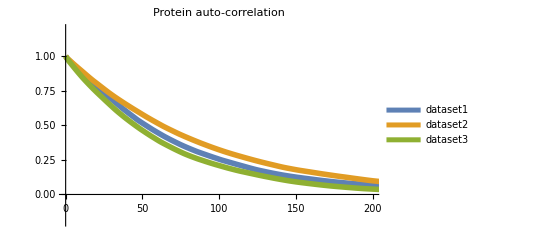

```mathematica
ListLinePlot[{Transpose@{Table[i,{i,0,Length[set1mcABiasedACFnoextrap]-1,1}],set1mcABiasedACFnoextrap},Transpose@{Table[i,{i,0,Length[set2mcABiasedACFnoextrap]-1,1}],set2mcABiasedACFnoextrap},Transpose@{Table[i,{i,0,Length[set3mcABiasedACFnoextrap]-1,1}],set3mcABiasedACFnoextrap}},PlotStyle->Directive[Thickness[0.01]],PlotLabel->Style["Protein auto-correlation",Black,16],AxesStyle->Directive[Black,16],PlotLegends->{"dataset1","dataset2","dataset3",Directive[Black,16]},PlotRange->{{0,200},{-.2,1.2}}]
```

```mathematica
Length[set1mcABiasedACFnoextrap]
```

402

```mathematica
Length[set2mcABiasedACFnoextrap]
```

402

```mathematica
Length[set3mcABiasedACFnoextrap]
```

396

```mathematica
meanproteinacf=Mean[{set1mcABiasedACFnoextrap[[1;;396]],set2mcABiasedACFnoextrap[[1;;396]],set3mcABiasedACFnoextrap[[1;;396]]}];
```

```mathematica
errorproteinacf=StandardDeviation[{set1mcABiasedACFnoextrap[[1;;396]],set2mcABiasedACFnoextrap[[1;;396]],set3mcABiasedACFnoextrap[[1;;396]]}];
```

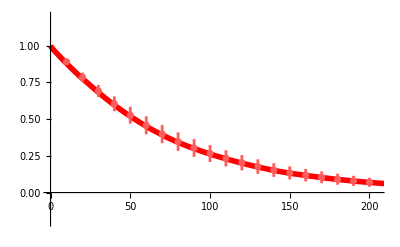

```mathematica
Show[
ListLinePlot[Transpose@{Table[i,{i,0,Length[meanproteinacf]-1,1}],meanproteinacf},PlotStyle->Directive[Thickness[0.01],Red],AxesStyle->Directive[Black,16],PlotRange->{{0,205},{-.2,1.2}}],ListPlot[Transpose@{Table[i,{i,0,200,10}],Map[Around[meanproteinacf[[#]],errorproteinacf[[#]]]&,Table[i,{i,0,200,10}]]},Axes->False,PlotRange->{{0,205},{-.2,1.2}},PlotStyle->Directive[Thickness[0.005],RGBColor[1,0.36,0.36]]]]
```

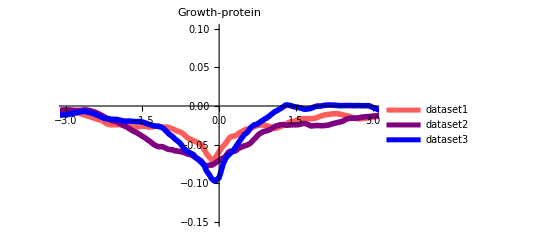

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,-(Length[set1mcgrowthABACFnoextrap]-1)/2,(Length[set1mcgrowthABACFnoextrap]-1)/2}],set1mcgrowthABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set2mcgrowthABACFnoextrap]-1)/2,(Length[set2mcgrowthABACFnoextrap]-1)/2}],set2mcgrowthABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set3mcgrowthABACFnoextrap]-1)/2,(Length[set3mcgrowthABACFnoextrap]-1)/2}],set3mcgrowthABACFnoextrap}},PlotRange->{{-3,3},{-.15,.1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.36,0.36]],Directive[Thickness[0.01],Purple],Directive[Thickness[0.01],Blue]}, PlotLegends->{"dataset1","dataset2","dataset3",Directive[Black,16]},PlotLabel->Style["Growth-protein",Black,16],AxesStyle->Directive[Black,16]]
```

```mathematica
meanproteingrowthccf=Mean[{set1mcgrowthABACFnoextrap[[1;;791]],set2mcgrowthABACFnoextrap[[1;;791]],set3mcgrowthABACFnoextrap[[1;;791]]}];
```

```mathematica
Length[set3mcgrowthABACFnoextrap]
```

791

```mathematica
errorproteingrowthccf=StandardDeviation[{set1mcgrowthABACFnoextrap[[1;;791]],set2mcgrowthABACFnoextrap[[1;;791]],set3mcgrowthABACFnoextrap[[1;;791]]}];
```

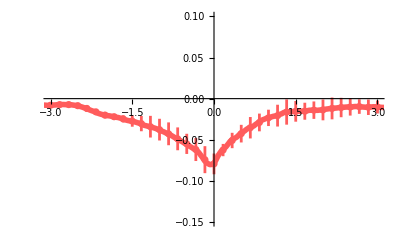

```mathematica
Show[
ListLinePlot[Transpose@{Table[i/60,{i,-(Length[meanproteingrowthccf]-1)/2,(Length[meanproteingrowthccf]-1)/2}],meanproteingrowthccf},PlotRange->{{-3,3},{-.15,.1}},PlotStyle->Directive[Thickness[0.01],RGBColor[1,0.36,0.36]],AxesStyle->Directive[Black,16]],
ListPlot[Transpose@{Table[i,{i,-3,3,1/6}],Map[Around[meanproteingrowthccf[[#]],errorproteingrowthccf[[#]]]&,Table[i,{i,395-180,395+180,10}]]},Axes->False,PlotRange->{{-3,3},{-.15,.1}},PlotStyle->Directive[Thickness[0.005],RGBColor[1,0.36,0.36]]]]
```

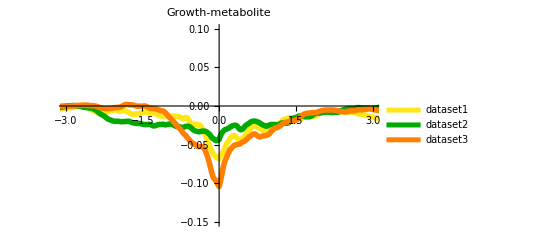

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,-(Length[set1betaxgrowthABACFnoextrap]-1)/2,(Length[set1betaxgrowthABACFnoextrap]-1)/2}],set1betaxgrowthABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set2betaxgrowthABACFnoextrap]-1)/2,(Length[set2betaxgrowthABACFnoextrap]-1)/2}],set2betaxgrowthABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set3betaxgrowthABACFnoextrap]-1)/2,(Length[set3betaxgrowthABACFnoextrap]-1)/2}],set3betaxgrowthABACFnoextrap}},PlotRange->{{-3,3},{-.15,.1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],Darker[Green]],Directive[Thickness[0.01],Orange]},PlotLegends->{"dataset1","dataset2","dataset3",Directive[Black,16]},PlotLabel->Style["Growth-metabolite",Black,16],AxesStyle->Directive[Black,16]]
```

```mathematica
Length[set3betaxgrowthABACFnoextrap]
```

791

```mathematica
meanmetagrowthccf=Mean[{set1betaxgrowthABACFnoextrap[[1;;791]],set2betaxgrowthABACFnoextrap[[1;;791]],set3betaxgrowthABACFnoextrap[[1;;791]]}];
```

```mathematica
errormetagrowthccf=StandardDeviation[{set1betaxgrowthABACFnoextrap[[1;;791]],set2betaxgrowthABACFnoextrap[[1;;791]],set3betaxgrowthABACFnoextrap[[1;;791]]}];
```

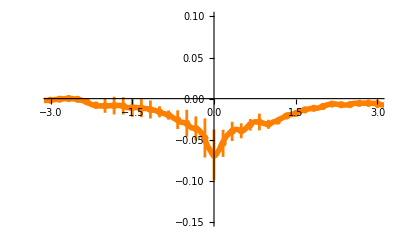

```mathematica
Show[
ListLinePlot[Transpose@{Table[i/60,{i,-(Length[meanmetagrowthccf]-1)/2,(Length[meanmetagrowthccf]-1)/2}],meanmetagrowthccf},PlotRange->{{-3,3},{-.15,.1}},PlotStyle->Directive[Thickness[0.01],Orange],AxesStyle->Directive[Black,16]],
ListPlot[Transpose@{Table[i,{i,-3,3,1/6}],Map[Around[meanmetagrowthccf[[#]],errormetagrowthccf[[#]]]&,Table[i,{i,395-180,395+180,10}]]},Axes->False,PlotRange->{{-3,3},{-.15,.1}},PlotStyle->Directive[Thickness[0.005],Orange]]]
```

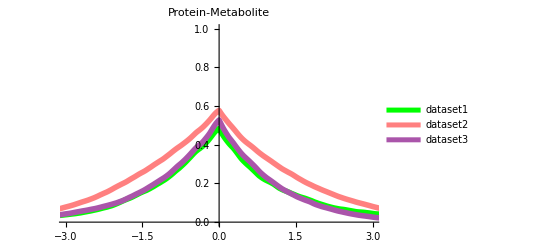

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,-(Length[set1mcbetaxABACFnoextrap]-1)/2,(Length[set1mcbetaxABACFnoextrap]-1)/2}],set1mcbetaxABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set2mcbetaxABACFnoextrap]-1)/2,(Length[set2mcbetaxABACFnoextrap]-1)/2}],set2mcbetaxABACFnoextrap},Transpose@{Table[i/60,{i,-(Length[set3mcbetaxABACFnoextrap]-1)/2,(Length[set3mcbetaxABACFnoextrap]-1)/2}],set3mcbetaxABACFnoextrap}},PlotRange->{{-3,3},{0,1}},PlotStyle->{Directive[Thickness[0.01],Green],Directive[Thickness[0.01],Pink],Directive[Thickness[0.01],Lighter[Purple]]}, PlotLegends->{"dataset1","dataset2","dataset3",Directive[Black,16]},PlotLabel->Style["Protein-Metabolite",Black,16],AxesStyle->Directive[Black,16]]
```

```mathematica
meanmetaproccf=Mean[{set1mcbetaxABACFnoextrap[[1;;791]],set2mcbetaxABACFnoextrap[[1;;791]],set3mcbetaxABACFnoextrap[[1;;791]]}];
```

```mathematica
errormetaproccf=StandardDeviation[{set1mcbetaxABACFnoextrap[[1;;791]],set2mcbetaxABACFnoextrap[[1;;791]],set3mcbetaxABACFnoextrap[[1;;791]]}];
```

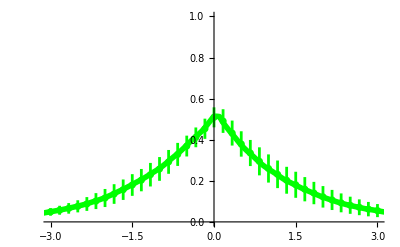

```mathematica
Show[
ListLinePlot[Transpose@{Table[i/60,{i,-(Length[meanmetaproccf]-1)/2,(Length[meanmetaproccf]-1)/2}],meanmetaproccf},PlotRange->{{-3,3},{0,1}},PlotStyle->Directive[Thickness[0.01],Green],AxesStyle->Directive[Black,16]],
ListPlot[Transpose@{Table[i,{i,-3,3,1/6}],Map[Around[meanmetaproccf[[#]],errormetaproccf[[#]]]&,Table[i,{i,395-180,395+180,10}]]},Axes->False,PlotRange->{{-3,3},{0,1}},PlotStyle->Directive[Thickness[0.005],Green]]]
```

```mathematica
test630=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\1000umclistaltalt.txt","Table"];
```

```mathematica
test6300=test630[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]=Round[test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]];
```

```mathematica
test6300[[2;;Length[test6300],{8}]]=N[test6300[[2;;Length[test6300],{8}]]-750];
```

```mathematica
test6300[[2;;Length[test6300],{10}]]=N[test6300[[2;;Length[test6300],{10}]]-963];
```

```mathematica
test6300[[2;;Length[test6300],{3}]]=N[test6300[[2;;Length[test6300],{3}]]*1/60];
```

```mathematica
test6300cut=removefljumps[test6300];
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

```mathematica
linstest6300cut=lineagefinder[test6300cut];//AbsoluteTiming
```

{9.17989,Null}

```mathematica
comblintest630=combinelineages2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{16.6501,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{15.5837,Null}

```mathematica
Length[comblinmultiplytest630]
```

387

```mathematica
sets630=Partition[RandomSample[Range[387]],129,129,129];
```

```mathematica
comblin630set1=Map[comblintest630[[#]]&,sets630[[1]]];
```

```mathematica
comblin630set2=Map[comblintest630[[#]]&,sets630[[2]]];comblin630set3=Map[comblintest630[[#]]&,sets630[[3]]];
```

```mathematica
comblin630multiplyset1=Map[comblinmultiplytest630[[#]]&,sets630[[1]]];
```

```mathematica
comblin630multiplyset2=Map[comblinmultiplytest630[[#]]&,sets630[[2]]];comblin630multiplyset3=Map[comblinmultiplytest630[[#]]&,sets630[[3]]];
```

```mathematica
growth630set1noextrap=growthratecalcsupnoextrap[comblin630multiplyset1,30,comblin630set1];//AbsoluteTiming
```

129

{1.14958,Null}

```mathematica
growth630set2noextrap=growthratecalcsupnoextrap[comblin630multiplyset2,30,comblin630set2];//AbsoluteTiming
```

129

{1.09645,Null}

```mathematica
growth630set3noextrap=growthratecalcsupnoextrap[comblin630multiplyset3,30,comblin630set3];//AbsoluteTiming
```

129

{1.02784,Null}

```mathematica
growth630set1cellphasenoextrap=addcellphase[growth630set1noextrap];//AbsoluteTiming
```

{0.0400176,Null}

```mathematica
growth630set2cellphasenoextrap=addcellphase[growth630set2noextrap];//AbsoluteTiming
growth630set3cellphasenoextrap=addcellphase[growth630set3noextrap];//AbsoluteTiming
```

{0.0408492,Null}

{0.0256268,Null}

```mathematica
avgcellphase630set1nofit=averagecellphasenofitting[growth630set1cellphasenoextrap,20];
```

```mathematica
avgcellphase630set2nofit=averagecellphasenofitting[growth630set2cellphasenoextrap,20];
avgcellphase630set3nofit=averagecellphasenofitting[growth630set3cellphasenoextrap,20];
```

```mathematica
avgcellphase630set1noextrap=averagecellphase[growth630set1cellphasenoextrap,growth630set1noextrap];//AbsoluteTiming
```

{1.91131,Null}

```mathematica
avgcellphase630set2noextrap=averagecellphase[growth630set2cellphasenoextrap,growth630set2noextrap];//AbsoluteTiming
```

{1.88327,Null}

```mathematica
avgcellphase630set3noextrap=averagecellphase[growth630set3cellphasenoextrap,growth630set3noextrap];//AbsoluteTiming
```

{1.93634,Null}

```mathematica
normcellphase630set1noextrap=normcellphase[avgcellphase630set1noextrap,growth630set1cellphasenoextrap];//AbsoluteTiming
```

{0.22293,Null}

```mathematica
normcellphase630set2noextrap=normcellphase[avgcellphase630set2noextrap,growth630set2cellphasenoextrap];//AbsoluteTiming
```

{0.247437,Null}

```mathematica
normcellphase630set3noextrap=normcellphase[avgcellphase630set3noextrap,growth630set3cellphasenoextrap];//AbsoluteTiming
```

{0.222404,Null}

```mathematica
combnormcellphase630set1noextrap=combnormcellphase[normcellphase630set1noextrap,growth630set1noextrap];//AbsoluteTiming
```

{0.118705,Null}

```mathematica
combnormcellphase630set2noextrap=combnormcellphase[normcellphase630set2noextrap,growth630set2noextrap];//AbsoluteTiming
```

{0.121011,Null}

```mathematica
combnormcellphase630set3noextrap=combnormcellphase[normcellphase630set3noextrap,growth630set3noextrap];//AbsoluteTiming
```

{0.107175,Null}

```mathematica
{avggrowthplot630set1noextrap,avgmcplot630set1noextrap,avgbetaxplot630set1noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphase630set1noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphase630set1noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphase630set1noextrap]]};//AbsoluteTiming
```

{3.66711,Null}

```mathematica
{avggrowthplot630set2noextrap,avgmcplot630set2noextrap,avgbetaxplot630set2noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphase630set2noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphase630set2noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphase630set2noextrap]]};//AbsoluteTiming
```

{3.81362,Null}

```mathematica
{avggrowthplot630set3noextrap,avgmcplot630set3noextrap,avgbetaxplot630set3noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphase630set3noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphase630set3noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphase630set3noextrap]]};//AbsoluteTiming
```

{3.70576,Null}

```mathematica
{set1growth630withrepeatnoextrap,set1growth630withrepeatnosubnoextrap,set1mc630withrepeatnoextrap,set1mc630withrepeatnosubnoextrap,set1betax630withrepeatnoextrap,set1betax630withrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,10,avggrowthplot630set1noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,11,avgmcplot630set1noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,12,avgbetaxplot630set1noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphase630set1noextrap,12,0],12,5]};//AbsoluteTiming
```

{13.7258,Null}

```mathematica
{set2growth630withrepeatnoextrap,set2growth630withrepeatnosubnoextrap,set2mc630withrepeatnoextrap,set2mc630withrepeatnosubnoextrap,set2betax630withrepeatnoextrap,set2betax630withrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,10,avggrowthplot630set2noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,11,avgmcplot630set2noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,12,avgbetaxplot630set2noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphase630set2noextrap,12,0],12,5]};//AbsoluteTiming
```

{13.4673,Null}

```mathematica
{set3growth630withrepeatnoextrap,set3growth630withrepeatnosubnoextrap,set3mc630withrepeatnoextrap,set3mc630withrepeatnosubnoextrap,set3betax630withrepeatnoextrap,set3betax630withrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,10,avggrowthplot630set3noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,11,avgmcplot630set3noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,12,avgbetaxplot630set3noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphase630set3noextrap,12,0],12,5]};//AbsoluteTiming
```

{13.2148,Null}

```mathematica
SetSharedVariable[set1growth630withrepeatnoextrap,set1growth630withrepeatnosubnoextrap,set1mc630withrepeatnoextrap,set1mc630withrepeatnosubnoextrap,set1betax630withrepeatnoextrap,set1betax630withrepeatnosubnoextrap];
```

```mathematica
SetSharedVariable[set2growth630withrepeatnoextrap,set2growth630withrepeatnosubnoextrap,set2mc630withrepeatnoextrap,set2mc630withrepeatnosubnoextrap,set2betax630withrepeatnoextrap,set2betax630withrepeatnosubnoextrap];
```

```mathematica
SetSharedVariable[set3growth630withrepeatnoextrap,set3growth630withrepeatnosubnoextrap,set3mc630withrepeatnoextrap,set3mc630withrepeatnosubnoextrap,set3betax630withrepeatnoextrap,set3betax630withrepeatnosubnoextrap];
```

```mathematica
DistributeDefinitions[austinUBcompositecrosscorrvars,austinBIASEDcompositecrosscorrvars,individualaustinUBcompositecrosscorrvars,individualaustinBIASEDcompositecrosscorrvars];
```

```mathematica
(*For[i=1,i<=Length[acetatemcwithrepeatnoextrap],i++,
acetatemcwithrepeatnoextrap[[i]][[All,2]]=GaussianFilter[acetatemcwithrepeatnoextrap[[i]][[All,2]],5];];
```

```mathematica
For[i=1,i<=Length[set1betax630withrepeatnoextrap],i++,
set1betax630withrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set1betax630withrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
For[i=1,i<=Length[set2betax630withrepeatnoextrap],i++,
set2betax630withrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set2betax630withrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
For[i=1,i<=Length[set3betax630withrepeatnoextrap],i++,
set3betax630withrepeatnoextrap[[i]][[All,2]]=GaussianFilter[set3betax630withrepeatnoextrap[[i]][[All,2]],3];];
```

```mathematica
{set1growthABiasedACF630noextrap,set1mcABiasedACF630noextrap,set1betaxABiasedACF630noextrap,set1mcgrowthABACF630noextrap,set1betaxgrowthABACF630noextrap,set1mcbetaxABACF630noextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set1growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set1mc630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set1betax630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1mc630withrepeatnoextrap,set1growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1betax630withrepeatnoextrap,set1growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set1mc630withrepeatnoextrap,set1betax630withrepeatnoextrap]}];//AbsoluteTiming
```

{329.724,Null}

```mathematica
{set2growthABiasedACF630noextrap,set2mcABiasedACF630noextrap,set2betaxABiasedACF630noextrap,set2mcgrowthABACF630noextrap,set2betaxgrowthABACF630noextrap,set2mcbetaxABACF630noextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set2growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set2mc630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set2betax630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2mc630withrepeatnoextrap,set2growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2betax630withrepeatnoextrap,set2growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set2mc630withrepeatnoextrap,set2betax630withrepeatnoextrap]}];//AbsoluteTiming
```

{296.692,Null}

```mathematica
{set3growthABiasedACF630noextrap,set3mcABiasedACF630noextrap,set3betaxABiasedACF630noextrap,set3mcgrowthABACF630noextrap,set3betaxgrowthABACF630noextrap,set3mcbetaxABACF630noextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[set3growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set3mc630withrepeatnoextrap],austinBIASEDcompositecrosscorrvars[set3betax630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3mc630withrepeatnoextrap,set3growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3betax630withrepeatnoextrap,set3growth630withrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[set3mc630withrepeatnoextrap,set3betax630withrepeatnoextrap]}];//AbsoluteTiming
```

{304.665,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Randomsubset630.txt",{set1growthABiasedACF630noextrap,set1mcABiasedACF630noextrap,set1betaxABiasedACF630noextrap,set1mcgrowthABACF630noextrap,set1betaxgrowthABACF630noextrap,set1mcbetaxABACF630noextrap,set2growthABiasedACF630noextrap,set2mcABiasedACF630noextrap,set2betaxABiasedACF630noextrap,set2mcgrowthABACF630noextrap,set2betaxgrowthABACF630noextrap,set2mcbetaxABACF630noextrap,set3growthABiasedACF630noextrap,set3mcABiasedACF630noextrap,set3betaxABiasedACF630noextrap,set3mcgrowthABACF630noextrap,set3betaxgrowthABACF630noextrap,set3mcbetaxABACF630noextrap},"Table"];
```

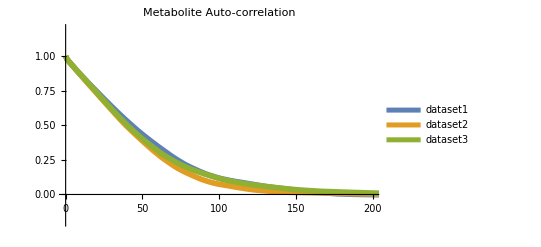

```mathematica
ListLinePlot[{Transpose@{Table[i,{i,0,Length[set1mcABiasedACF630noextrap]-1,1}],set1mcABiasedACF630noextrap},Transpose@{Table[i,{i,0,Length[set2mcABiasedACF630noextrap]-1,1}],set2mcABiasedACF630noextrap},Transpose@{Table[i,{i,0,Length[set3mcABiasedACF630noextrap]-1,1}],set3mcABiasedACF630noextrap}},PlotStyle->Directive[Thickness[0.01]],PlotLabel->Style["Metabolite Auto-correlation",Black,16],AxesStyle->Directive[Black,16],PlotLegends->{"dataset1","dataset2","dataset3",Directive[Black,16]},PlotRange->{{0,200},{-.2,1.2}}]
```

```mathematica
Length[set3mcABiasedACF630noextrap]
```

244

```mathematica
meanmetaacf=Mean[{set1mcABiasedACF630noextrap[[1;;236]],set2mcABiasedACF630noextrap[[1;;236]],set3mcABiasedACF630noextrap[[1;;236]]}];
errormetaacf=StandardDeviation[{set1mcABiasedACF630noextrap[[1;;236]],set2mcABiasedACF630noextrap[[1;;236]],set3mcABiasedACF630noextrap[[1;;236]]}];
```

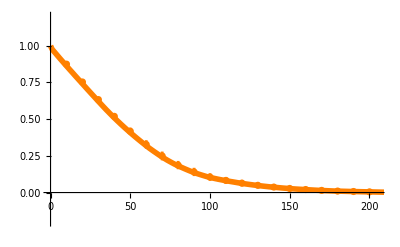

```mathematica
Show[
ListLinePlot[Transpose@{Table[i,{i,0,Length[meanmetaacf]-1,1}],meanmetaacf},PlotStyle->Directive[Thickness[0.01],Orange],AxesStyle->Directive[Black,16],PlotRange->{{0,205},{-.2,1.2}}],ListPlot[Transpose@{Table[i,{i,0,200,10}],Map[Around[meanmetaacf[[#]],errormetaacf[[#]]]&,Table[i,{i,0,200,10}]]},Axes->False,PlotRange->{{0,205},{-.2,1.2}},PlotStyle->Directive[Thickness[0.005],Orange]]]
```